```mathematica
1+1
```

2

```mathematica
f[x_]=x Exp[-x]
```

ⅇ^-x x

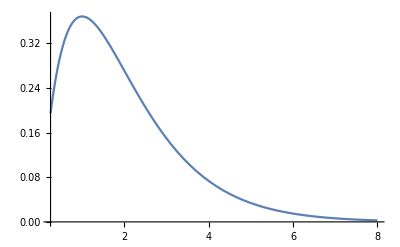

```mathematica
Plot[f[x],{x,0.25,8}]
```

```mathematica
data=Table[{x,f[x]},{x,0.25,8,0.25}]
```

{{0.25,0.1947},{0.5,0.303265},{0.75,0.354275},{1.,0.367879},{1.25,0.358131},{1.5,0.334695},{1.75,0.304104},{2.,0.270671},{2.25,0.237148},{2.5,0.205212},{2.75,0.175802},{3.,0.149361},{3.25,0.126016},{3.5,0.105691},{3.75,0.0881915},{4.,0.0732626},{4.25,0.060623},{4.5,0.0499905},{4.75,0.0410956},{5.,0.0336897},{5.25,0.0275495},{5.5,0.0224772},{5.75,0.018301},{6.,0.0148725},{6.25,0.0120653},{6.5,0.00977235},{6.75,0.00790344},{7.,0.00638317},{7.25,0.00514876},{7.5,0.00414813},{7.75,0.00333825},{8.,0.0026837}}

```mathematica
(* test 1 *)
```

```mathematica
model6=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6},x]
```

0.0413503+0.78334 x-0.639247 x^2+0.214195 x^3-0.0365134 x^4+0.00312821 x^5-0.000106855 x^6

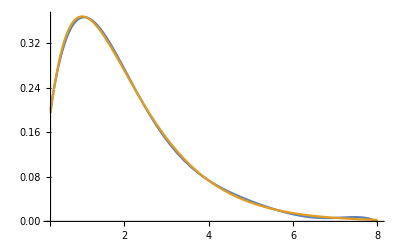

```mathematica
Plot[{model6,f[x]},{x,0.25,8}]
```

```mathematica
(* Relative error *)
```

```mathematica
Dif6[x_]=1-model6/f[x]
```

1-(ⅇ^x (0.0413503+0.78334 x-0.639247 x^2+0.214195 x^3-0.0365134 x^4+0.00312821 x^5-0.000106855 x^6))/x

```mathematica
Res6=Table[{x,Dif6[x]},{x,0.25,8,0.25}]
```

{{0.25,-0.0294778},{0.5,0.0180319},{0.75,0.0154185},{1.,0.00471174},{1.25,-0.00534755},{1.5,-0.011819},{1.75,-0.0137013},{2.,-0.0110135},{2.25,-0.0045101},{2.5,0.00444576},{2.75,0.0139941},{3.,0.0219359},{3.25,0.0259708},{3.5,0.0240337},{3.75,0.0147321},{4.,-0.00213692},{4.25,-0.025048},{4.5,-0.0502929},{4.75,-0.071781},{5.,-0.0813411},{5.25,-0.0698379},{5.5,-0.0294523},{5.75,0.0425899},{6.,0.138838},{6.25,0.235667},{6.5,0.288692},{6.75,0.234418},{7.,0.00794717},{7.25,-0.404856},{7.5,-0.847915},{7.75,-0.75167},{8.,1.3289}}

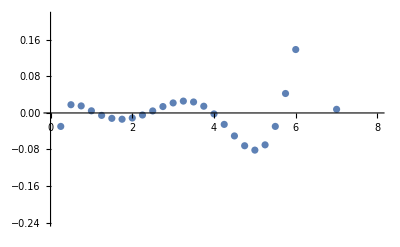

```mathematica
pl6=ListPlot[Res6]
```

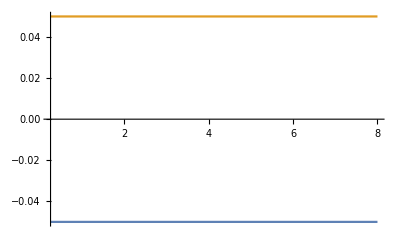

```mathematica
pl2=Plot[{-0.05,0.05},{x,0.25,8}]
```

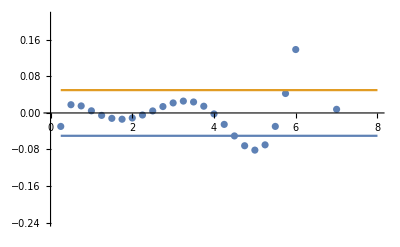

```mathematica
Show[pl6,pl2]
```

```mathematica
(* Test 2 *)
```

```mathematica
model8=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

0.00510219+0.965461 x-0.920558 x^2+0.410944 x^3-0.109336 x^4+0.0183283 x^5-0.00189896 x^6+0.000110944 x^7-2.79068×10^-6 x^8

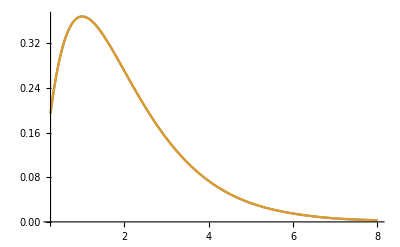

```mathematica
Plot[{model8,f[x]},{x,0.25,8}]
```

```mathematica
Dif8[x_]=1-model8/f[x]
```

1-(ⅇ^x (0.00510219+0.965461 x-0.920558 x^2+0.410944 x^3-0.109336 x^4+0.0183283 x^5-0.00189896 x^6+0.000110944 x^7-2.79068×10^-6 x^8))/x

```mathematica
Res8=Table[{x,Dif8[x]},{x,0.25,8,0.25}]
```

{{0.25,-0.00125244},{0.5,0.00162707},{0.75,0.00026003},{1.,-0.000738595},{1.25,-0.000892151},{1.5,-0.00041944},{1.75,0.000299606},{2.,0.00089651},{2.25,0.0011024},{2.5,0.000800606},{2.75,0.0000502187},{3.,-0.000922769},{3.25,-0.00177149},{3.5,-0.00211239},{3.75,-0.00164109},{4.,-0.000262814},{4.25,0.00179375},{4.5,0.00392324},{4.75,0.0052044},{5.,0.00462417},{5.25,0.00148688},{5.5,-0.00403428},{5.75,-0.0103608},{6.,-0.014307},{6.25,-0.011713},{6.5,0.000502251},{6.75,0.0205497},{7.,0.0370993},{7.25,0.0277697},{7.5,-0.0279648},{7.75,-0.0952612},{8.,0.06546}}

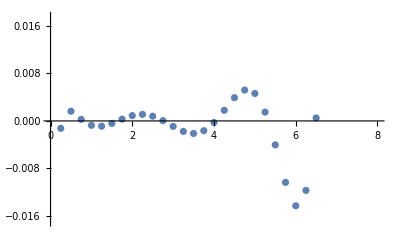

```mathematica
pl8=ListPlot[Res8]
```

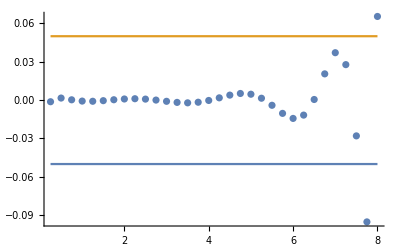

```mathematica
Show[pl8,pl2,PlotRange->All]
```